```mathematica
w[θ_,a_]:= Sqrt[1-a Sin[θ]^2] /2/Pi
Integrate[w[θ,0.5],{θ,0,2 Pi},Assumptions->{Reals,0<a<1}]
```

0.859847

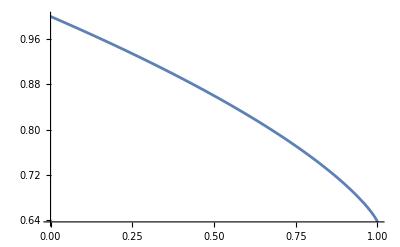

```mathematica
Plot[Integrate[w[θ,a],{θ,0,2 Pi},Assumptions->{Reals,0<a<1}],{a,0,1}]
```

```mathematica
Plot[NIntegrate[w[θ,a],{θ,0,2 Pi}],{a,0,1}]
```

-Graphics-

```mathematica
Integrate[w[θ,0],{θ,0,2 Pi}]
```

NIntegrate::inumr: 在以 {{0,6.28319}} 为界的区域内，对于所有采样点，计算被积函数 (√(1-0.0000204286 Sin[θ]^2))/(2 （ ） π) 得到非数值.

NIntegrate::inumr: 在以 {{0.,6.28319}} 为界的区域内，对于所有采样点，计算被积函数 (√(1-0.0000204286 Sin[θ]^2))/(2 （ ） π) 得到非数值.

NIntegrate::inumr: 在以 {{0,6.28319}} 为界的区域内，对于所有采样点，计算被积函数 (√(1-0.0204286 Sin[θ]^2))/(2 （ ） π) 得到非数值.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

-Graphics-

1/(（ ）)

```mathematica
Integrate[w[θ,r],{θ,0,2 Pi},Reals]
```

$Aborted

```mathematica
Integrate[w[θ,r],{θ,0,2 Pi}]
```

ConditionalExpression[(2 (-v0+v1) (EllipticE[(3 π)/4-ϕ/2,(2 r^2)/(r^2-R^2)]+EllipticE[1/4 (π+2 ϕ),(2 r^2)/(r^2-R^2)]) √(R^2+r^2 Sin[ϕ]))/(v1 √((R^2+r^2 Sin[ϕ])/(-r^2+R^2))), ]

```mathematica
FullSimplify[(2 (-v0+v1) (EllipticE[(3 π)/4-ϕ/2,(2 r^2)/(r^2-R^2)]+EllipticE[1/4 (π+2 ϕ),(2 r^2)/(r^2-R^2)]) √(R^2+r^2 Sin[ϕ]))/(v1 √((R^2+r^2 Sin[ϕ])/(-r^2+R^2))),Assumptions->{Reals,r>0,R>0}]
```

```mathematica
(2 (-v0+v1) (EllipticE[(3 π)/4-ϕ/2,(2 r^2)/(r^2-R^2)]+EllipticE[1/4 (π+2 ϕ),(2 r^2)/(r^2-R^2)]) √(R^2+r^2 Sin[ϕ]))/(v1 √((R^2+r^2 Sin[ϕ])/(-r^2+R^2)))
```

```mathematica
FullSimplify[(2 (-v0+v1) (EllipticE[(3 π)/4-ϕ/2,(2 r^2)/(r^2-R^2)]+EllipticE[1/4 (π+2 ϕ),(2 r^2)/(r^2-R^2)]) √(R^2+r^2 Sin[ϕ]))/(v1 √((R^2+r^2 Sin[ϕ])/(-r^2+R^2))) == (2 (-v0+v1) (EllipticE[(3 π)/4-ϕ/2,(2 r^2)/(r^2-R^2)]+EllipticE[1/4 (π+2 ϕ),(2 r^2)/(r^2-R^2)]))/(v1 √(1/(-r^2+R^2))),Assumptions->{Reals,R > 10 r}]
```

((v0-v1) (EllipticE[(3 π)/4-ϕ/2,(2 r^2)/(r^2-R^2)]+EllipticE[1/4 (π+2 ϕ),(2 r^2)/(r^2-R^2)]) (-√(1/(-r^2+R^2)) √(R^2+r^2 Sin[ϕ])+√((R^2+r^2 Sin[ϕ])/(-r^2+R^2))))/(v1 √((R^2+r^2 Sin[ϕ])/(-r^2+R^2)))==0

```mathematica
Integrate[w[θ,10^-10],{θ,0,2 Pi}]
```

```mathematica
-(((v0-v1) (EllipticE[1/4 (3 π-2 ϕ),2/(1-100000000000000000000 R^2)]+EllipticE[1/4 (π+2 ϕ),2/(1-100000000000000000000 R^2)]) √(100000000000000000000 R^2+Sin[ϕ]))/(5000000000 v1 √((100000000000000000000 R^2+Sin[ϕ])/(-1+100000000000000000000 R^2))))
```

```mathematica
FullSimplify[-(((v0-v1) (EllipticE[1/4 (3 π-2 ϕ),2/(1-100000000000000000000 R^2)]+EllipticE[1/4 (π+2 ϕ),2/(1-100000000000000000000 R^2)]) √(100000000000000000000 R^2+Sin[ϕ]))/(5000000000 v1 √((100000000000000000000 R^2+Sin[ϕ])/(-1+100000000000000000000 R^2)))),Reals]
```

-((v0-v1) (EllipticE[1/4 (3 π-2 ϕ),2/(1-100000000000000000000 R^2)]+EllipticE[1/4 (π+2 ϕ),2/(1-100000000000000000000 R^2)]) √(100000000000000000000 R^2+Sin[ϕ]))/(5000000000 v1 √((100000000000000000000 R^2+Sin[ϕ])/(-1+100000000000000000000 R^2)))

```mathematica
wfull[θ_,r_,R_,v0_,v1_,ϕ_]:= (1-v0/v1)Sqrt[R^2-r^2 Sin[θ - ϕ]] - r Cos[θ-ϕ]
```

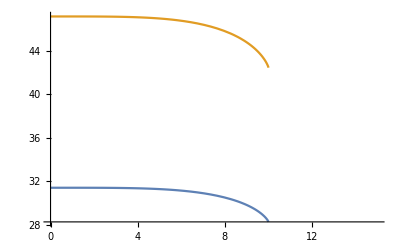

```mathematica
Plot[{NIntegrate[wfull[θ,r,10,1,2,0],{θ,0,2 Pi}],NIntegrate[wfull[θ,r,10,1,4,0],{θ,0,2 Pi}]},{r,0,15}]
```

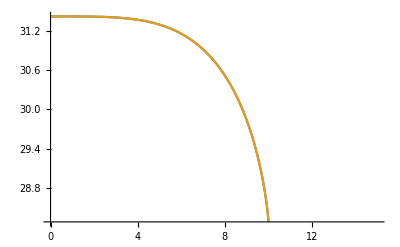

```mathematica
Plot[{NIntegrate[wfull[θ,r,10,1,2,0],{θ,0,2 Pi}],NIntegrate[wfull[θ,r,10,1,2,2Pi/3],{θ,0,2 Pi}]},{r,0,15}]
```

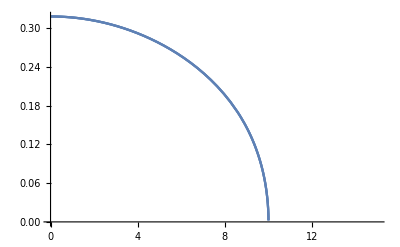

```mathematica
Plot[ {1/(EllipticE[(3 π)/4-ϕ/2,(2 r^2)/(r^2-R^2)]+EllipticE[1/4 (π+2 ϕ),(2 r^2)/(r^2-R^2)])/.ϕ->0,1/(EllipticE[(3 π)/4-ϕ/2,(2 r^2)/(r^2-R^2)]+EllipticE[1/4 (π+2 ϕ),(2 r^2)/(r^2-R^2)])/.ϕ->1,1/(EllipticE[(3 π)/4-ϕ/2,(2 r^2)/(r^2-R^2)]+EllipticE[1/4 (π+2 ϕ),(2 r^2)/(r^2-R^2)])/.ϕ->2}/.{R->10},{r,0,15}]
```

```mathematica
Series[(2 (-v0+v1) (EllipticE[(3 π)/4-ϕ/2,(2 r^2)/(r^2-R^2)]+EllipticE[1/4 (π+2 ϕ),(2 r^2)/(r^2-R^2)]) √(R^2+r^2 Sin[ϕ]))/(v1 √((R^2+r^2 Sin[ϕ])/(-r^2+R^2))),{1/r,0,2}]
```

General::ivar: 1/r is not a valid variable.

```mathematica
FullSimplify[Series[(2 (-v0+v1) (EllipticE[(3 π)/4-ϕ/2,(2 r^2)/(r^2-R^2)]+EllipticE[1/4 (π+2 ϕ),(2 r^2)/(r^2-R^2)]) √(R^2+r^2 Sin[ϕ]))/(v1 √((R^2+r^2 Sin[ϕ])/(-r^2+R^2))),{r,0,25}]]
```

(2 π √(R^2) (-v0+v1))/v1+(π (v0-v1) r^4)/(8 (R^2)^(3/2) v1)+(15 π √(R^2) (v0-v1) r^8)/(512 R^8 v1)+(105 π √(R^2) (v0-v1) r^12)/(8192 R^12 v1)+(15015 π √(R^2) (v0-v1) r^16)/(2097152 R^16 v1)+(153153 π √(R^2) (v0-v1) r^20)/(33554432 R^20 v1)+(6789783 π √(R^2) (v0-v1) r^24)/(2147483648 R^24 v1)+O[r]^26

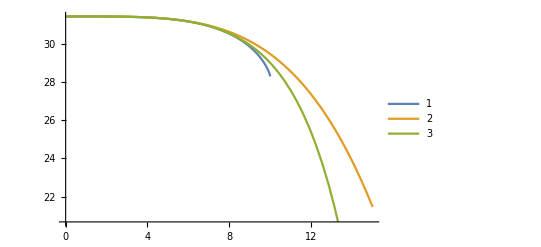

```mathematica
Plot[{NIntegrate[wfull[θ,r,10,1,2,1],{θ,0,2 Pi}],(2 π √(R^2) (-v0+v1))/v1+(π (v0-v1) r^4)/(8 (R^2)^(3/2) v1)/.{R->10,v0->1,v1->2,ϕ->1},(2 π √(R^2) (-v0+v1))/v1+(π (v0-v1) r^4)/(8 (R^2)^(3/2) v1)+(15 π √(R^2) (v0-v1) r^8)/(512 R^8 v1)/.{R->10,v0->1,v1->2,ϕ->1}},{r,0,15},PlotLegends->Automatic]
```